```mathematica
AppendTo[$Path,NotebookDirectory[]];
Needs["PenroseTilingFunctions`"]
```

```mathematica
Inflate[starseed,1]
```

{{{0.809017+0.587785 ⅈ,0,0.618034},fat},{{0.618034,1,0.809017+0.587785 ⅈ},skinny},{{1.30902+0.951057 ⅈ,1,0.809017+0.587785 ⅈ},fat},{{0.809017+0.587785 ⅈ,0,0.190983+0.587785 ⅈ},fat},{{0.190983+0.587785 ⅈ,0.309017+0.951057 ⅈ,0.809017+0.587785 ⅈ},skinny},{{1.30902+0.951057 ⅈ,0.309017+0.951057 ⅈ,0.809017+0.587785 ⅈ},fat},{{-0.309017+0.951057 ⅈ,0,0.190983+0.587785 ⅈ},fat},{{0.190983+0.587785 ⅈ,0.309017+0.951057 ⅈ,-0.309017+0.951057 ⅈ},skinny},{{-0.5+1.53884 ⅈ,0.309017+0.951057 ⅈ,-0.309017+0.951057 ⅈ},fat},{{-0.309017+0.951057 ⅈ,0,-0.5+0.363271 ⅈ},fat},{{-0.5+0.363271 ⅈ,-0.809017+0.587785 ⅈ,-0.309017+0.951057 ⅈ},skinny},{{-0.5+1.53884 ⅈ,-0.809017+0.587785 ⅈ,-0.309017+0.951057 ⅈ},fat},{{-1.,0,-0.5+0.363271 ⅈ},fat},{{-0.5+0.363271 ⅈ,-0.809017+0.587785 ⅈ,-1.},skinny},{{-1.61803,-0.809017+0.587785 ⅈ,-1.},fat}}

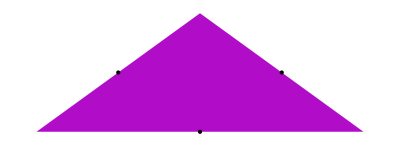

```mathematica
Show[See@{unitfat},Graphics[Point/@Coor@Midpoints[unitfat]]]
```

```mathematica
??IfFat
```

T if the triangle is fat, F if skinny

IfFat[t_,T_,F_]:=If[Last[t]==fat,T,F]

Rhomb[{{a_,b_,c_},f_}]:={{a,a-c+b,b,c},f}

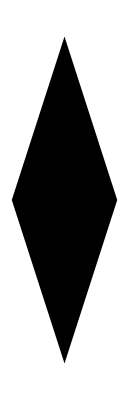

```mathematica
Graphics[(Polygon/@Coor/@PathTriangles@Rhomb@unitskinny)]
```

```mathematica
TestPoints:=Graphics@{Yellow,EdgeForm[Black],{Triangle@Coor@ #,{PointSize[Large],Transpose[{{Red,Green,Blue},Point/@Coor@#}]}}}&
```

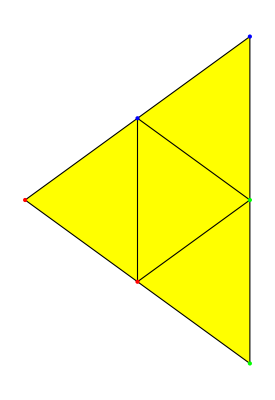
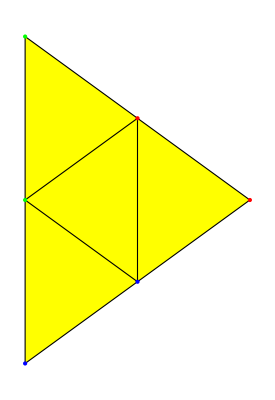

```mathematica
Show/@Transpose[{TestPoints/@(PathTriangles@Rhomb@unitfat),TestPoints/@(Midpoints/@PathTriangles@Rhomb@unitfat)}]
```

```mathematica
Midpoints/@PathTriangles@Rhomb@unitskinny
```

{{0.,0.25+0.769421 ⅈ,-0.25+0.769421 ⅈ},{-0.25-0.769421 ⅈ,0.25-0.769421 ⅈ,0.}}

```mathematica
Midpoints[{A_,B_,C_}]:=1/2{B+A,B+C,A+C}

Orientation[{A_,B_,C_}]:=Sign@Det[{Flatten@Coor@{B-A},Flatten@Coor@{((C-B))}}]

OrientTriangle[{A_,B_,C_}]:=If[Orientation[{A,B,C}]==1,{A,B,C},{A,C,B}]

PathTriangles[{{A_,P_,B_,C_},t_}]:=If[t=="fat",{{A,P,C},{B,C,P}},{{A,B,C},{A,P,B}}]

MakePathTriangles[list_]:=OrientTriangle/@Flatten[PathTriangles/@list,1]

EqualQ[list_,element_]:=Equal[#,element]&/@list

SharedSide[list_,element_]:=Select[list,MemberQ[EqualQ[#,element],True]&]

FindNextTriangle[list_,prev_,midpoint_]:=DeleteCases[SharedSide[list,midpoint],prev]

ChangeTriangle[list_,prev_,midpoint_]:=Flatten@FindNextTriangle[list,prev,midpoint]

PathStep[list_,{starttriangle_,startmidpoint_,dir_}]:=
Module[{nexttriangle,nextmidpoint,startside=First@Flatten@Position[SetPrecision[#,10]&/@starttriangle,SetPrecision[startmidpoint,10]],nextdir=-1*dir},nextmidpoint=Go[{starttriangle,startside},dir];
{ChangeTriangle[list,starttriangle,nextmidpoint],nextmidpoint,nextdir}]

MakePath[list_,{starttriangle_,startmidpoint_,dir_}]:=NestWhileList[PathStep[list,#]&,{starttriangle,startmidpoint,dir},FreeQ[{}]]
```

```mathematica
Midpoints/@PathTriangles@Rhomb@unitskinny
FindNextTriangle[%,%[[1]],0.]
```

```mathematica
ChangeTriangle[Midpoints/@PathTriangles@Rhomb@unitskinny,{0.,0.25+0.7694208842938134 ⅈ,-0.25+0.7694208842938134 ⅈ},0.]
```

{-0.25-0.769421 ⅈ,0.25-0.769421 ⅈ,0.}

```mathematica
GoRight[{{-0.25-0.7694208842938134 ⅈ,0.25-0.7694208842938134 ⅈ,0.},3}]
```

-0.25-0.769421 ⅈ

```mathematica
testtris=Midpoints/@PathTriangles@Rhomb@unitskinny
```

{{0.,0.25+0.769421 ⅈ,-0.25+0.769421 ⅈ},{-0.25-0.769421 ⅈ,0.25-0.769421 ⅈ,0.}}

```mathematica
First@Flatten@Position[{0.,0.25+0.7694208842938134 ⅈ,-0.25+0.7694208842938134 ⅈ},0.25+0.7694208842938134 ⅈ]
```

```mathematica
nxt=Go[{{0.,0.25+0.7694208842938134 ⅈ,-0.25+0.7694208842938134 ⅈ},2},-1]
```

```mathematica
ChangeTriangle[testtris,testtris[[1]],nxt]
```

{-0.25-0.769421 ⅈ,0.25-0.769421 ⅈ,0.}

```mathematica
PathStep[testtris,{testtris[[1]],testtris[[1,2]]},-1]
```

{{-0.25-0.769421 ⅈ,0.25-0.769421 ⅈ,0.},0.,1}

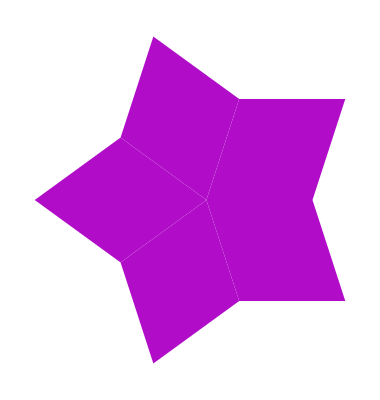

```mathematica
See@(FullInflate[starseed,0])
```

```mathematica
testtris=Midpoints/@MakePathTriangles@FullInflate[starseed,1]

PathStep[testtris,{testtris[[1]],testtris[[1,2]],1}]
```

{{-1.52254-0.293893 ⅈ,-1.21353-0.293893 ⅈ,-1.30902},{-0.904508-0.293893 ⅈ,-1.21353-0.293893 ⅈ,-1.11803-0.587785 ⅈ},{-1.30902,-1.21353+0.293893 ⅈ,-1.52254+0.293893 ⅈ},{-1.11803+0.587785 ⅈ,-1.21353+0.293893 ⅈ,-0.904508+0.293893 ⅈ},{-0.75-0.181636 ⅈ,-0.5+0. ⅈ,-0.75+0.181636 ⅈ},{-0.25+0.181636 ⅈ,-0.5+0. ⅈ,-0.25-0.181636 ⅈ},{-0.404508-1.24495 ⅈ,-0.654508-1.06331 ⅈ,-0.75-1.35721 ⅈ},{-0.904508-0.881678 ⅈ,-0.654508-1.06331 ⅈ,-0.559017-0.769421 ⅈ},{-0.190983-1.53884 ⅈ,-0.0954915-1.24495 ⅈ,-0.404508-1.24495 ⅈ},{0.-0.951057 ⅈ,-0.0954915-1.24495 ⅈ,0.213525-1.24495 ⅈ},{-0.75+1.35721 ⅈ,-0.654508+1.06331 ⅈ,-0.404508+1.24495 ⅈ},{-0.559017+0.769421 ⅈ,-0.654508+1.06331 ⅈ,-0.904508+0.881678 ⅈ},{-0.404508+1.24495 ⅈ,-0.0954915+1.24495 ⅈ,-0.190983+1.53884 ⅈ},{0.213525+1.24495 ⅈ,-0.0954915+1.24495 ⅈ,0.+0.951057 ⅈ},{-0.75-0.181636 ⅈ,-0.904508-0.293893 ⅈ,-0.654508-0.475528 ⅈ},{-0.654508-0.475528 ⅈ,-0.559017-0.769421 ⅈ,-0.404508-0.657164 ⅈ},{-0.654508+0.475528 ⅈ,-0.904508+0.293893 ⅈ,-0.75+0.181636 ⅈ},{-0.404508+0.657164 ⅈ,-0.559017+0.769421 ⅈ,-0.654508+0.475528 ⅈ},{-0.059017-0.769421 ⅈ,-0.154508-0.475528 ⅈ,-0.404508-0.657164 ⅈ},{-0.25-0.181636 ⅈ,-0.154508-0.475528 ⅈ,0.0954915-0.293893 ⅈ},{-0.404508+0.657164 ⅈ,-0.154508+0.475528 ⅈ,-0.059017+0.769421 ⅈ},{0.0954915+0.293893 ⅈ,-0.154508+0.475528 ⅈ,-0.25+0.181636 ⅈ},{-0.059017-0.769421 ⅈ,0.-0.951057 ⅈ,0.25-0.769421 ⅈ},{0.25-0.769421 ⅈ,0.559017-0.769421 ⅈ,0.5-0.587785 ⅈ},{0.25+0.769421 ⅈ,0.+0.951057 ⅈ,-0.059017+0.769421 ⅈ},{0.5+0.587785 ⅈ,0.559017+0.769421 ⅈ,0.25+0.769421 ⅈ},{0.713525-0.293893 ⅈ,0.904508-0.293893 ⅈ,0.809017},{0.809017,0.904508+0.293893 ⅈ,0.713525+0.293893 ⅈ},{0.713525-0.293893 ⅈ,0.404508-0.293893 ⅈ,0.5-0.587785 ⅈ},{0.0954915-0.293893 ⅈ,0.404508-0.293893 ⅈ,0.309017-1.11022×10^-16 ⅈ},{0.5+0.587785 ⅈ,0.404508+0.293893 ⅈ,0.713525+0.293893 ⅈ},{0.309017+1.11022×10^-16 ⅈ,0.404508+0.293893 ⅈ,0.0954915+0.293893 ⅈ},{1.05902-0.769421 ⅈ,0.809017-0.951057 ⅈ,1.05902-1.13269 ⅈ},{0.559017-1.13269 ⅈ,0.809017-0.951057 ⅈ,0.559017-0.769421 ⅈ},{1.40451-0.657164 ⅈ,1.15451-0.475528 ⅈ,1.05902-0.769421 ⅈ},{0.904508-0.293893 ⅈ,1.15451-0.475528 ⅈ,1.25-0.181636 ⅈ},{1.05902+1.13269 ⅈ,0.809017+0.951057 ⅈ,1.05902+0.769421 ⅈ},{0.559017+0.769421 ⅈ,0.809017+0.951057 ⅈ,0.559017+1.13269 ⅈ},{1.05902+0.769421 ⅈ,1.15451+0.475528 ⅈ,1.40451+0.657164 ⅈ},{1.25+0.181636 ⅈ,1.15451+0.475528 ⅈ,0.904508+0.293893 ⅈ}}

{{-1.30902,-1.21353+0.293893 ⅈ,-1.52254+0.293893 ⅈ},-1.30902,-1}

```mathematica
testtris[[3,1]]
```

```mathematica
Point[Coor@{testtris[[3,1]]}]
```

Point[{{-1.52254,0.293893}}]

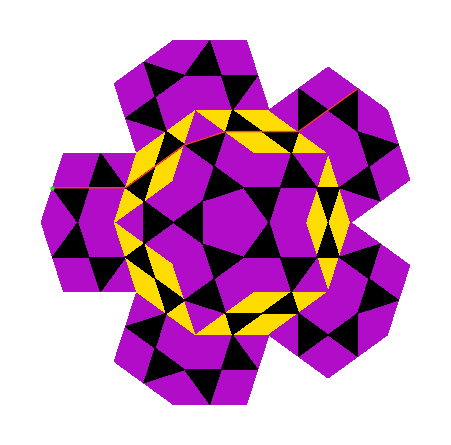

```mathematica
Show[See@(FullInflate[starseed,1]),SeeTri/@testtris,Graphics[{NiceRed,Thick,#}]&/@PathPoints@MakePath[testtris,{testtris[[3]],testtris[[3,3]],-1}],Graphics[{Thick,Green,Point[Coor@{testtris[[3,3]]}]}]]
```

```mathematica
TableForm[testtris]
MakePath[testtris,{testtris[[3]],testtris[[3,3]],-1}]
```

-1.52254-0.293893 ⅈ | -1.21353-0.293893 ⅈ | -1.30902
-0.904508-0.293893 ⅈ | -1.21353-0.293893 ⅈ | -1.11803-0.587785 ⅈ
-1.30902 | -1.21353+0.293893 ⅈ | -1.52254+0.293893 ⅈ
-1.11803+0.587785 ⅈ | -1.21353+0.293893 ⅈ | -0.904508+0.293893 ⅈ
-0.75-0.181636 ⅈ | -0.5+0. ⅈ | -0.75+0.181636 ⅈ
-0.25+0.181636 ⅈ | -0.5+0. ⅈ | -0.25-0.181636 ⅈ
-0.404508-1.24495 ⅈ | -0.654508-1.06331 ⅈ | -0.75-1.35721 ⅈ
-0.904508-0.881678 ⅈ | -0.654508-1.06331 ⅈ | -0.559017-0.769421 ⅈ
-0.190983-1.53884 ⅈ | -0.0954915-1.24495 ⅈ | -0.404508-1.24495 ⅈ
0.-0.951057 ⅈ | -0.0954915-1.24495 ⅈ | 0.213525-1.24495 ⅈ
-0.75+1.35721 ⅈ | -0.654508+1.06331 ⅈ | -0.404508+1.24495 ⅈ
-0.559017+0.769421 ⅈ | -0.654508+1.06331 ⅈ | -0.904508+0.881678 ⅈ
-0.404508+1.24495 ⅈ | -0.0954915+1.24495 ⅈ | -0.190983+1.53884 ⅈ
0.213525+1.24495 ⅈ | -0.0954915+1.24495 ⅈ | 0.+0.951057 ⅈ
-0.75-0.181636 ⅈ | -0.904508-0.293893 ⅈ | -0.654508-0.475528 ⅈ
-0.654508-0.475528 ⅈ | -0.559017-0.769421 ⅈ | -0.404508-0.657164 ⅈ
-0.654508+0.475528 ⅈ | -0.904508+0.293893 ⅈ | -0.75+0.181636 ⅈ
-0.404508+0.657164 ⅈ | -0.559017+0.769421 ⅈ | -0.654508+0.475528 ⅈ
-0.059017-0.769421 ⅈ | -0.154508-0.475528 ⅈ | -0.404508-0.657164 ⅈ
-0.25-0.181636 ⅈ | -0.154508-0.475528 ⅈ | 0.0954915-0.293893 ⅈ
-0.404508+0.657164 ⅈ | -0.154508+0.475528 ⅈ | -0.059017+0.769421 ⅈ
0.0954915+0.293893 ⅈ | -0.154508+0.475528 ⅈ | -0.25+0.181636 ⅈ
-0.059017-0.769421 ⅈ | 0.-0.951057 ⅈ | 0.25-0.769421 ⅈ
0.25-0.769421 ⅈ | 0.559017-0.769421 ⅈ | 0.5-0.587785 ⅈ
0.25+0.769421 ⅈ | 0.+0.951057 ⅈ | -0.059017+0.769421 ⅈ
0.5+0.587785 ⅈ | 0.559017+0.769421 ⅈ | 0.25+0.769421 ⅈ
0.713525-0.293893 ⅈ | 0.904508-0.293893 ⅈ | 0.809017
0.809017 | 0.904508+0.293893 ⅈ | 0.713525+0.293893 ⅈ
0.713525-0.293893 ⅈ | 0.404508-0.293893 ⅈ | 0.5-0.587785 ⅈ
0.0954915-0.293893 ⅈ | 0.404508-0.293893 ⅈ | 0.309017-1.11022×10^-16 ⅈ
0.5+0.587785 ⅈ | 0.404508+0.293893 ⅈ | 0.713525+0.293893 ⅈ
0.309017+1.11022×10^-16 ⅈ | 0.404508+0.293893 ⅈ | 0.0954915+0.293893 ⅈ
1.05902-0.769421 ⅈ | 0.809017-0.951057 ⅈ | 1.05902-1.13269 ⅈ
0.559017-1.13269 ⅈ | 0.809017-0.951057 ⅈ | 0.559017-0.769421 ⅈ
1.40451-0.657164 ⅈ | 1.15451-0.475528 ⅈ | 1.05902-0.769421 ⅈ
0.904508-0.293893 ⅈ | 1.15451-0.475528 ⅈ | 1.25-0.181636 ⅈ
1.05902+1.13269 ⅈ | 0.809017+0.951057 ⅈ | 1.05902+0.769421 ⅈ
0.559017+0.769421 ⅈ | 0.809017+0.951057 ⅈ | 0.559017+1.13269 ⅈ
1.05902+0.769421 ⅈ | 1.15451+0.475528 ⅈ | 1.40451+0.657164 ⅈ
1.25+0.181636 ⅈ | 1.15451+0.475528 ⅈ | 0.904508+0.293893 ⅈ

{{{-1.30902,-1.21353+0.293893 ⅈ,-1.52254+0.293893 ⅈ},-1.52254+0.293893 ⅈ,-1},{{-1.11803+0.587785 ⅈ,-1.21353+0.293893 ⅈ,-0.904508+0.293893 ⅈ},-1.21353+0.293893 ⅈ,1},{{-0.654508+0.475528 ⅈ,-0.904508+0.293893 ⅈ,-0.75+0.181636 ⅈ},-0.904508+0.293893 ⅈ,-1},{{-0.404508+0.657164 ⅈ,-0.559017+0.769421 ⅈ,-0.654508+0.475528 ⅈ},-0.654508+0.475528 ⅈ,1},{{-0.404508+0.657164 ⅈ,-0.154508+0.475528 ⅈ,-0.059017+0.769421 ⅈ},-0.404508+0.657164 ⅈ,-1},{{0.25+0.769421 ⅈ,0.+0.951057 ⅈ,-0.059017+0.769421 ⅈ},-0.059017+0.769421 ⅈ,1},{{},{0.25+0.769421 ⅈ,0.+0.951057 ⅈ,-0.059017+0.769421 ⅈ}⟦Mod[1+First[{}],3,1]⟧,-1}}

```mathematica
PathStep[testtris,{{0.25+0.7694208842938133 ⅈ,0.+0.9510565162951535 ⅈ,-0.05901699437494744+0.7694208842938133 ⅈ},-0.05901699437494748+0.7694208842938133 ⅈ,1}]
```

{First[{}],{},{},-1}

```mathematica
Go[{{0.25+0.7694208842938133 ⅈ,0.+0.9510565162951535 ⅈ,-0.05901699437494744+0.7694208842938133 ⅈ},3},1]
```

0.25+0.769421 ⅈ

```mathematica
Position[SetPrecision[#,10]&/@{0.25+0.7694208842938133 ⅈ,0.+0.9510565162951535 ⅈ,-0.05901699437494744+0.7694208842938133 ⅈ},SetPrecision[-0.05901699437494748+0.7694208842938133 ⅈ,10]]
```

{{3}}

```mathematica
SetPrecision[-0.05901699437494744+0.7694208842938133 ⅈ,4]
```

-0.059+0.7694 ⅈ

```mathematica
SetPrecision[-0.05901699437494744+0.7694208842938133 ⅈ,5]
```

-0.05902+0.76942 ⅈ

```mathematica
SetPrecision[-0.05901699437494744+0.7694208842938133 ⅈ,10]===SetPrecision[-0.05901699437494748+0.7694208842938133 ⅈ,10]
```

True

```mathematica
RoundComplex[num_,n_]:=Complex[N[Re[num],n],N[Im[num],n]]
```

```mathematica
RoundComplex[-0.05901699437494744+0.7694208842938133 ⅈ,2]
```

-0.059017+0.769421 ⅈ

```mathematica
N[-0.05901699437494744+0.7694208842938133 ⅈ,1]===N[-0.05901699437494748+0.7694208842938133 ⅈ,1]
```

False

```mathematica
N[-0.05901699437494744,2]
```

-0.059017

```mathematica
-0.05901699437494744+0.7694208842938133 ⅈ
-0.05901699437494748+0.7694208842938133 ⅈ
```

-0.059017+0.769421 ⅈ

-0.059017+0.769421 ⅈ

```mathematica
FullForm[-0.05901699437494744+0.7694208842938133 ⅈ]
FullForm[-0.05901699437494748+0.7694208842938133 ⅈ]
```

Complex[-0.059017,0.769421]

Complex[-0.059017,0.769421]

```mathematica
Position[{a,b,c,2,2.},2]
```

{{4}}

```mathematica
SharedSide[testtris,-0.05901699437494748+0.7694208842938133 ⅈ]
```

{{-0.404508+0.657164 ⅈ,-0.154508+0.475528 ⅈ,-0.059017+0.769421 ⅈ},{0.25+0.769421 ⅈ,0.+0.951057 ⅈ,-0.059017+0.769421 ⅈ}}

```mathematica
ChangeTriangle[testtris,{0.25+0.7694208842938133 ⅈ,0.+0.9510565162951535 ⅈ,-0.05901699437494744+0.7694208842938133 ⅈ},-0.05901699437494748+0.7694208842938133 ⅈ]
```

```mathematica
Flatten@Position[{-0.4045084971874737+0.657163890148917 ⅈ,-0.15450849718747373+0.47552825814757677 ⅈ,-0.05901699437494748+0.7694208842938133 ⅈ},-0.05901699437494748+0.7694208842938133 ⅈ]
```

{3}

```mathematica
MemberQ[testtris[[25]],]
```

True

```mathematica
MemberQ[testtris[[25]],_==testtris[[25,3]]]
```

False

```mathematica
{-0.05901699437494748+0.769420884293813 ⅈ==testtris[[25,3]]}
```

{True}

```mathematica
MemberQ[{1,1.,2},Equal[_,2.]]
```

False

```mathematica
Select[{{1,2.,3},{1,2,2.},{A,b,c}},MemberQ[EqualQ[#,2],True]&]
```

{{1,2.,3},{1,2,2.}}

```mathematica
MemberQ[EqualQ[{1,2.,3},2],True]
```

True

```mathematica
2==2.
```

True

```mathematica
2==2.
```

True

```mathematica
testtris[[25,3]]==testtris[[21,3]]
```

True

False

```mathematica
SharedSide[testtris,-0.05901699437494748+0.7694208842938133 ⅈ]
Position[testtris,#]&/@%
```

{{-0.404508+0.657164 ⅈ,-0.154508+0.475528 ⅈ,-0.059017+0.769421 ⅈ},{0.25+0.769421 ⅈ,0.+0.951057 ⅈ,-0.059017+0.769421 ⅈ}}

{{{21}},{{25}}}

{{{-0.904508+0.293893 ⅈ,-1.21353+0.293893 ⅈ,-1.11803+0.587785 ⅈ},-0.904508+0.293893 ⅈ,1},{{-1.52254+0.293893 ⅈ,-1.21353+0.293893 ⅈ,-1.30902},-1.21353+0.293893 ⅈ,-1},{{},-1.52254+0.293893 ⅈ,1}}

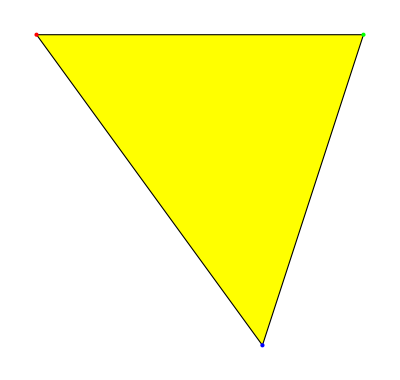
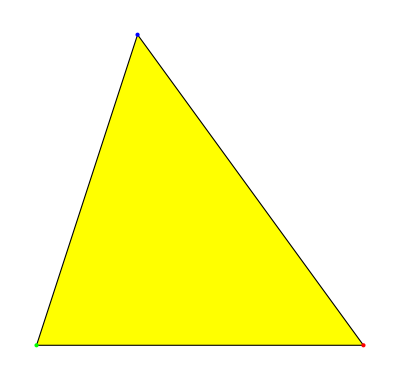
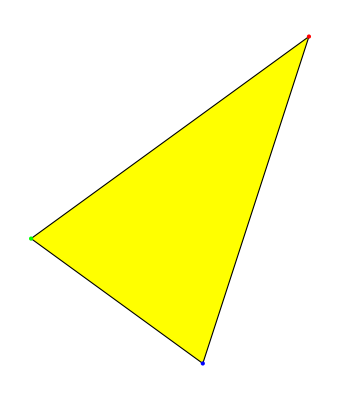
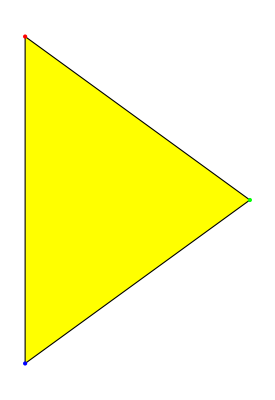
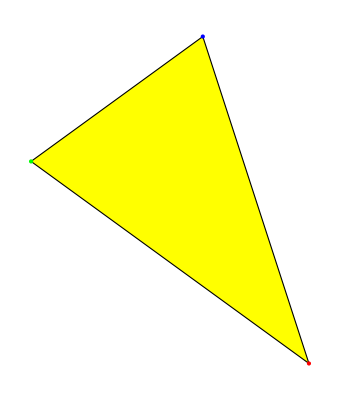
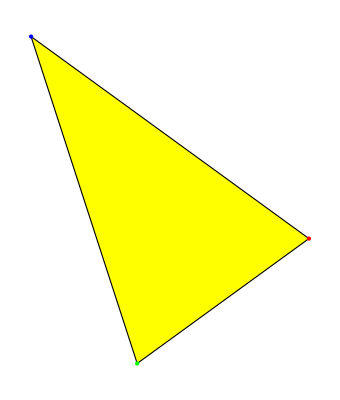
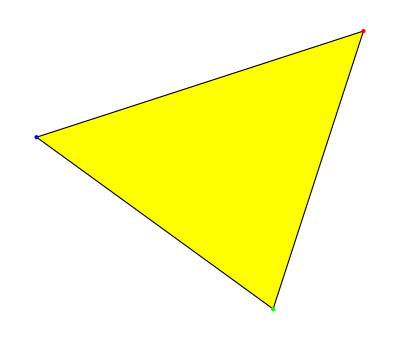
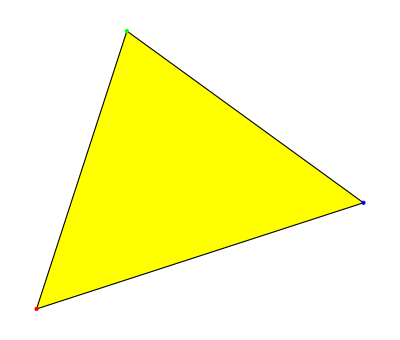

```mathematica
MakePath[testtris,{testtris[[4]],testtris[[4,1]],1}]
```

```mathematica
MakePath[testtris,{testtris[[7]],testtris[[7,1]],1}];
TestPoints/@Most@%[[All,1]]
Orientation/@Most@%%[[All,1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-1,-1,-1,-1,-1,1,-1,-1}

```mathematica
Coor[{0.30901699437494745+0. ⅈ}]
```

{{0.309017,0.}}

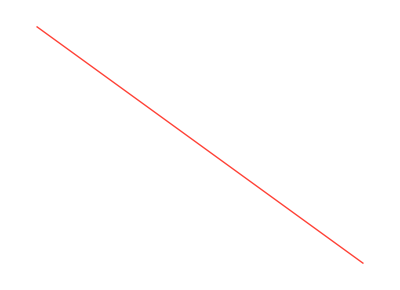
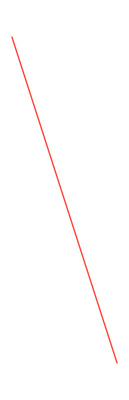
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Graphics[{NiceRed,Thick,#}]&/@PathPoints@MakePath[testtris,{testtris[[3]],testtris[[3,1]],-1}]
```

```mathematica
PathPoints[list_]:=Line/@Partition[Coor@list[[All,2]],2,1]
```

```mathematica
SeeTri[points_]:=Graphics@Polygon@Coor@points
```

```mathematica
Line
```

```mathematica
TestPointsRhombs:=Graphics@{Yellow,EdgeForm[Black],{Polygon@Coor@ #,{PointSize[Large],Transpose[{{Red,Green,Blue,Purple},Point/@Coor@#}]}}}&
```

```mathematica
FullInflate[{unitfat},0]
```

{{{-0.809017,-1.11022×10^-16+0.587785 ⅈ,0.809017,1.11022×10^-16-0.587785 ⅈ},fat}}

```mathematica
TestPointsRhombs:=Graphics@{Yellow,EdgeForm[Black],{Polygon@Coor@ #,{PointSize[Large],Transpose[{{Red,Green,Blue,Purple},Point/@Coor@#}]}}}&
```